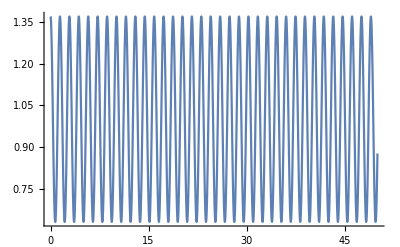

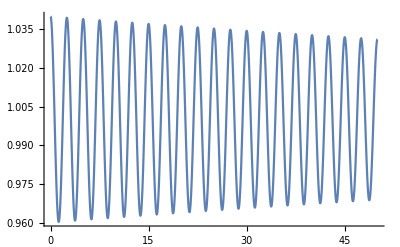

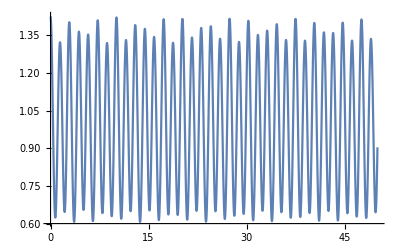

```mathematica
Acbo = 0.04;
taucbo = 200;
Tcbo = 2.5;
wa = 4.36;
A = 0.37;


f[t_]:=1+A*Cos[wa*t];
Plot[f[x],{x,0,50}]
cbo[t_]:=1+Acbo*Exp[-t/taucbo]*Cos[(2*Pi/Tcbo)*t];
Plot[cbo[x],{x,0,50}]
Plot[f[x]*cbo[x],{x,0,50}]
```